Mathematica >

# 关于九宫格密码盘的研究

The functions defined in the NumericalAnalysis` context provide support for finding numerical solutions to calculus-related problems.

This loads the package:

```mathematica
<<NumericalAnalysis`
```

## Numerical Calculation of Series Expansions

```mathematica
allPermutations=Permutations[Range[1,9],{2,9}];
invalidSegments={{1,3},{3,1},{4,6},{6,4},{7,9},{9,7},{1,7},{7,1},{2,8},{8,2},{3,9},{9,3},{1,9},{9,1},{3,7},{7,3}};
invalidPattern={Alternatives@@Apply[PatternSequence[Except[(#1+#2)/2]...,#1,#2]&,invalidSegments,{1}],___};
validPermutations=DeleteCases[allPermutations,invalidPattern];
Length[allPermutations]
Length[validPermutations]
Table[Length[Select[validPermutations,Length[#1]==i&]],{i,2,9}]
```

986400

389488

{56,320,1624,7152,26016,72912,140704,140704}

```mathematica
Graph[{1<->2,1<->4,1<->5,1<->6,1<->8,2<->3,2<->4,2<->5,2<->6,2<->7,2<->9,3<->4,3<->5,3<->6,3<->8,4<->5,4<->7,4<->8,4<->9,5<->6,5<->7,5<->8,5<->9,5<->9,6<->7,6<->8,6<->9,7<->8,8<->9},VertexLabels->"Name"]
```

Graph::supp: 不支持混合图和多图.

Graph[{1<->2,1<->4,1<->5,1<->6,1<->8,2<->3,2<->4,2<->5,2<->6,2<->7,2<->9,3<->4,3<->5,3<->6,3<->8,4<->5,4<->7,4<->8,4<->9,5<->6,5<->7,5<->8,5<->9,5<->9,6<->7,6<->8,6<->9,7<->8,8<->9},VertexLabels→Name]

```mathematica
(*2×2密码盘*)
ArrayPlot[{
{0,1,1,1},
{1,0,1,1},
{1,1,0,1},
{1,1,1,0}}]
```

-Graphics-

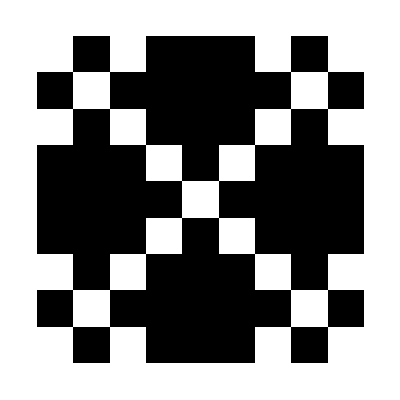

```mathematica
(*3×3密码盘*)
ArrayPlot[{
{0,1,0,1,1,1,0,1,0},
{1,0,1,1,1,1,1,0,1},
{0,1,0,1,1,1,0,1,0},
{1,1,1,0,1,0,1,1,1},
{1,1,1,1,0,1,1,1,1},
{1,1,1,0,1,0,1,1,1},
{0,1,0,1,1,1,0,1,0},
{1,0,1,1,1,1,1,0,1},
{0,1,0,1,1,1,0,1,0}}]
```

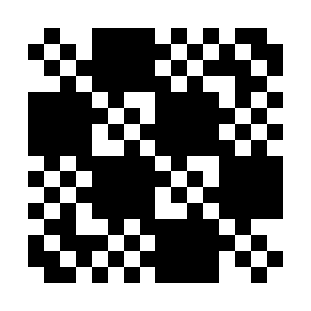

```mathematica
(*4×4密码盘*)
ArrayPlot[{
{0,1,0,0,1,1,1,1,0,1,0,1,0,1,1,0},{1,0,1,0,1,1,1,1,1,0,1,0,1,0,1,1},{0,1,0,1,1,1,1,1,0,1,0,1,1,1,0,1},{0,0,1,0,1,1,1,1,1,0,1,0,0,1,1,0},{1,1,1,1,0,1,0,0,1,1,1,1,0,1,0,1},{1,1,1,1,1,0,1,0,1,1,1,1,1,0,1,0},{1,1,1,1,0,1,0,1,1,1,1,1,0,1,0,1},{1,1,1,1,0,0,1,0,1,1,1,1,1,0,1,0},{0,1,0,1,1,1,1,1,0,1,0,0,1,1,1,1},{1,0,1,0,1,1,1,1,1,0,1,0,1,1,1,1},{0,1,0,1,1,1,1,1,0,1,0,1,1,1,1,1},{1,0,1,0,1,1,1,1,0,0,1,0,1,1,1,1},{0,1,1,0,0,1,0,1,1,1,1,1,0,1,0,0},{1,0,1,1,1,0,1,0,1,1,1,1,1,0,1,0},{1,1,0,1,0,1,0,1,1,1,1,1,0,1,0,1},{0,1,1,0,1,0,1,0,1,1,1,1,0,0,1,0}}]
```